```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
markers={"■","●","◆","▲","□","○","◇","△"}
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{■,●,◆,▲,□,○,◇,△}

## fig3a, fig3b

```mathematica
figID="3";
names={"3v","3s"};
d=Length@names;
errsFilePath="data\\fig"<>figID<>"-"<>#<>"-errs.csv"&/@names;
varsFilePath="data\\fig"<>figID<>"-"<>#<>"-vars.csv"&/@names;
errs=Import/@errsFilePath;
vars=Import/@varsFilePath;
x=errs[[1,1,2;;]];
y=errs[[1,2;;,1]];
errs=errs[[;;,2;;,2;;]]*100;
vars=vars[[;;,2;;,2;;]]*100;
uppers=errs+vars/2;
lowers=errs-vars/2;
Min[errs]
Max[errs]
```

0.535928984497126629

5.58389781237581609

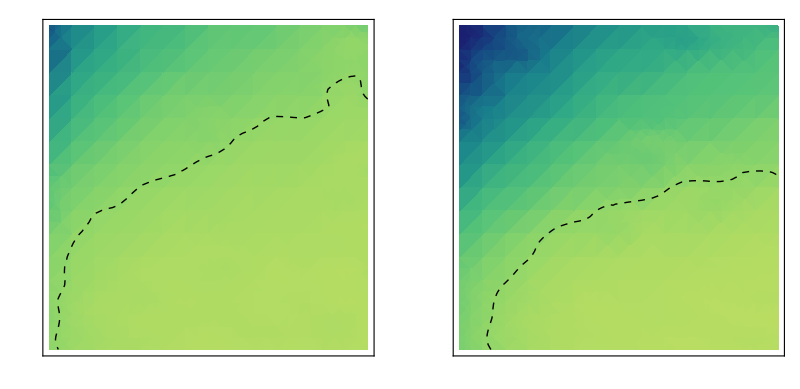

```mathematica
points=Flatten[Table[{x[[i]],y[[j]],#[[j,i]]},{i,Length@x},{j,Length@y}],1]&/@errs;
fs=Interpolation[#,InterpolationOrder->3]&/@points;
minVal=0;
maxVal=6;
ps=Module[{p1,p2,p},
p1=DensityPlot[#[x0,y0],{x0,x[[1]],x[[-1]]},{y0,y[[1]],y[[-1]]},PlotRange->All,PlotLegends->None,ColorFunction->Function[f,ColorData["BlueGreenYellow"][1-(f-minVal)/(maxVal-minVal)]],ColorFunctionScaling->False,FrameTicks->None];
p2=ContourPlot[#[x0,y0]==1,{x0,x[[1]],x[[-1]]},{y0,y[[1]],y[[-1]]-0.3*10^(-13)},ContourStyle->Directive[Black,Thick,Dashed]];
p=Show[p1,p2]
]&/@fs;
bar=BarLegend[{Function[f,ColorData["BlueGreenYellow"][1-(f-minVal)/(maxVal-minVal)]],{minVal,maxVal}}];
p3ab=GraphicsRow[Insert[ps,bar,-1],AspectRatio->1/2.5,ImageSize->Full]
```

```mathematica
Export["subplots\\fig3ab.png",p3ab]
```

subplots\fig3ab.png

## fig3c

```mathematica
x[[3]]
data1=errs[[;;,;;,3]];
lowers1=lowers[[;;,;;,3]];
uppers1=uppers[[;;,;;,3]];
data1=Transpose@{y,#}&/@data1;
lowers1=Transpose@{y,#}&/@lowers1;
uppers1=Transpose@{y,#}&/@uppers1;
```

64.

```mathematica
p1=ListPlot[Evaluate@(uppers1~Join~lowers1),Joined->True,PlotStyle->None,Filling->Table[{i->{{i+d},Directive[colors[[i]],Opacity[0.2]]}},{i,d}]];
p2=ListLinePlot[Evaluate@data1,PlotMarkers->markers,PlotStyle->colors,PlotTheme->"Scientific",GridLines->None];
p3c=Show[p1,p2,Axes->False,PlotRange->{{0,200}*10^(-15),{0,6}}]
```

-Graphics-

```mathematica
Export["subplots\\fig3c.png",p3c]
```

subplots\fig3c.png

## fig3d

```mathematica
y[[11]]
data2=errs[[;;,11,;;]];
lowers2=lowers[[;;,11,;;]];
uppers2=uppers[[;;,11,;;]];
data2=Transpose@{x,#}&/@data2;
lowers2=Transpose@{x,#}&/@lowers2;
uppers2=Transpose@{x,#}&/@uppers2;
```

1.00000000000000003×10^-13

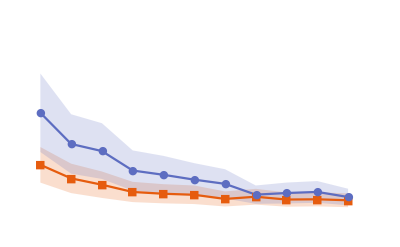

```mathematica
p1=ListPlot[Evaluate@(uppers2~Join~lowers2),Joined->True,PlotStyle->None,Filling->Table[{i->{{i+d},Directive[colors[[i]],Opacity[0.2]]}},{i,d}]];
p2=ListLinePlot[Evaluate@data2,PlotMarkers->markers,PlotStyle->colors,PlotTheme->"Scientific",GridLines->None];
p3d=Show[p1,p2,Axes->False,PlotRange->{{30,200},{0,6}}]
```

```mathematica
Export["subplots\\fig3d.png",p3d]
```

subplots\fig3d.png